```mathematica
ToVars3[g_]:=Block[{exp,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
exp= True;
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var =Symbol["x" <> ToString[ vertices[[vertex]] ]];
exp= exp&& Element[var, Integers];
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var =Symbol["x" <> ToString[ vertices[[vertex]] ]];
exp= exp&& (1≤ var <=4);
];

edges=EdgeList[g];

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 =Symbol["x" <> ToString[ edge[[1]] ]];
var2 =Symbol["x" <> ToString[ edge[[2]] ]];
exp= exp && var1!=var2;
];
exp
]
```

```mathematica
SymbolRange[n_]:=Table[Symbol["x"<>ToString[i]],{i,1,n}]
```

```mathematica
Take[deps3,-1]
```

{{15,49,{3,{3,2,7,8,6},{2<->6,2<->8},{{2,3,6},{2,6,8},{2,7,8}}}}}

```mathematica
ToVars3[ReadGrof[15]]
```

x1∈Integers&&x2∈Integers&&x3∈Integers&&x7∈Integers&&x6∈Integers&&x8∈Integers&&x4∈Integers&&x5∈Integers&&1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x7≤4&&1≤x6≤4&&1≤x8≤4&&1≤x4≤4&&1≤x5≤4&&x1≠x2&&x1≠x3&&x1≠x7&&x2≠x3&&x2≠x6&&x2≠x7&&x2≠x8&&x3≠x4&&x3≠x5&&x3≠x6&&x3≠x7&&x4≠x5&&x4≠x6&&x5≠x6&&x5≠x7&&x5≠x8&&x6≠x8&&x7≠x8

```mathematica
FullSimplify[ToVars3[ReadGrof[15]]]
```

x1∈Integers&&x2∈Integers&&x3∈Integers&&x7∈Integers&&x6∈Integers&&x8∈Integers&&x4∈Integers&&x5∈Integers&&1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x7≤4&&1≤x6≤4&&1≤x8≤4&&1≤x4≤4&&1≤x5≤4&&x1≠x2&&x1≠x3&&x1≠x7&&x2≠x3&&x2≠x6&&x2≠x7&&x2≠x8&&x3≠x4&&x3≠x5&&x3≠x6&&x3≠x7&&x4≠x5&&x4≠x6&&x5≠x6&&x5≠x7&&x5≠x8&&x6≠x8&&x7≠x8

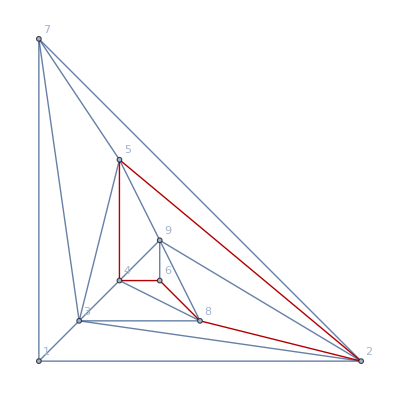

```mathematica
Graph[Rule3[ReadGrof[14],{5<->6,2<->6},{4,6,8,2,5}], VertexLabels->"Name", GraphLayout->"PlanarEmbedding", GraphHighlight->Rule3Cycle[{4,6,8,2,5}]]
```

```mathematica
Take[deps3,-10]
```

{{58716,398406,{3,{1,2,3,13,5},{2<->5,2<->13},{{1,2,5},{2,5,13},{2,3,13}}}},{58716,395242,{3,{1,5,9,13,2},{2<->5,5<->13},{{1,2,5},{2,5,13},{5,9,13}}}},{58716,398050,{3,{3,5,13,2,1},{1<->5,2<->5},{{1,3,5},{1,2,5},{2,5,13}}}},{58716,395284,{3,{9,3,6,10,7},{3<->7,3<->10},{{3,7,9},{3,7,10},{3,6,10}}}},{58716,398420,{3,{9,7,5,10,3},{3<->7,7<->10},{{3,7,9},{3,7,10},{5,7,10}}}},{58716,395243,{3,{7,3,2,13,9},{3<->9,3<->13},{{3,7,9},{3,9,13},{2,3,13}}}},{58716,398427,{3,{3,7,10,5,9},{7<->9,5<->7},{{3,7,9},{5,7,9},{5,7,10}}}},{58716,398413,{3,{3,9,13,5,7},{7<->9,5<->9},{{3,7,9},{5,7,9},{5,9,13}}}},{58716,395251,{3,{10,3,8,12,6},{3<->6,3<->12},{{3,6,10},{3,6,12},{3,8,12}}}},{58716,398408,{3,{3,11,8,5,4},{4<->11,5<->11},{{3,4,11},{4,5,11},{5,8,11}}}}}

```mathematica
MatrixForm[SolsToColors[Solve[ToVars3[EdgeDelete[ ReadGrof[14],{5<->6,2<->6}]]&&x4==1&&x6==2&&x8==3,SymbolRange[8]]]]
```

(RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1])

```mathematica
MatrixForm[SolsToColors[Solve[ToVars3[Rule3[ReadGrof[14],{5<->6,2<->6},{4,6,8,2,5}]]&&x4==1&&x6==2&&x8==3,SymbolRange[9]]]]
```

(RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0])

```mathematica
VarsToColors[l_]:=Map[IndexToColor[#[[2]]]&,Sort[l]]
```

```mathematica
SolsToColors[l_]:=Map[VarsToColors,l]
```

```mathematica
VarsToColors[{x6->4,x1->1,x2->2,x3->3,x4->1,x5->2,x7->4,x8->1}]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0]}

```mathematica
VarsToColors[{x6->4,x1->1,x2->2,x3->3,x4->1,x5->2,x7->4,x8->1}]
```

```mathematica
{"FrontierEdge"->(With[{edge=#},
Print[edge];
sols[[edge[[2]]]]=Intersection[sols[[edge[[2]]]],sols[[edge[[1]]]]]
])&}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0]}

```mathematica
Complement
```

```mathematica
DepthFirstScan[
```

```mathematica
ToVars4[g_]:=Block[{sols},
sols= Table[{1,2,3,4},{i,1,VertexCount[g]}];
sols[[1]]={1};

BreadthFirstScan[g,1,{"FrontierEdge"->(Print[#,sols[[#[[1]]]],sols[[#[[2]]]],sols[[#[[2]]]]=Complement[sols[[#[[2]]]],sols[[#[[1]]]]]]&)}];
Table[i->Row[Map[IndexToColor[#]&,sols[[i]]]],{i,1,VertexCount[g]}]
]
```

```mathematica
ToVars4[ReadGrof[15]]
```

1<->2{1}{1,2,3,4}{2,3,4}

1<->3{1}{1,2,3,4}{2,3,4}

1<->7{1}{1,2,3,4}{2,3,4}

2<->6{2,3,4}{1,2,3,4}{1}

2<->8{2,3,4}{1,2,3,4}{1}

3<->4{2,3,4}{1,2,3,4}{1}

3<->5{2,3,4}{1,2,3,4}{1}

{1→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0],3→RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0],4→RGBColor[1, 0, 0],5→RGBColor[1, 0, 0],6→RGBColor[1, 0, 0],7→RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0],8→RGBColor[1, 0, 0]}

1<->2{1}{1,2,3,4}{2,3,4}

1<->3{1}{1,2,3,4}{2,3,4}

1<->7{1}{1,2,3,4}{2,3,4}

2<->6{2,3,4}{1,2,3,4}{1}

2<->8{2,3,4}{1,2,3,4}{1}

3<->4{2,3,4}{1,2,3,4}{1}

3<->5{2,3,4}{1,2,3,4}{1}

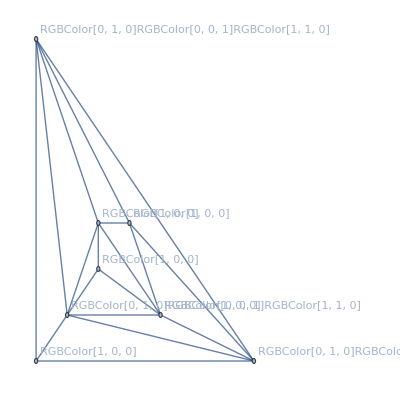

```mathematica
Graph[ReadGrof[15],VertexLabels->ToVars4[ReadGrof[15]], GraphLayout->"PlanarEmbedding"]
```

```mathematica
Solve[x1⊂{1,2,3,4}&&x2⊂{1,2,3,4}&&x3⊂{1,2,3,4}&&x7⊂{1,2,3,4}&&x6⊂{1,2,3,4}&&x8⊂{1,2,3,4}&&x4⊂{1,2,3,4}&&x5⊂{1,2,3,4}&&x1⊂Complement[{1,2,3,4},x2]&&x1⊂Complement[{1,2,3,4},x3]&&x1⊂Complement[{1,2,3,4},x7]&&x2⊂Complement[{1,2,3,4},x3]&&x2⊂Complement[{1,2,3,4},x6]&&x2⊂Complement[{1,2,3,4},x7]&&x2⊂Complement[{1,2,3,4},x8]&&x3⊂Complement[{1,2,3,4},x4]&&x3⊂Complement[{1,2,3,4},x5]&&x3⊂Complement[{1,2,3,4},x6]&&x3⊂Complement[{1,2,3,4},x7]&&x4⊂Complement[{1,2,3,4},x5]&&x4⊂Complement[{1,2,3,4},x6]&&x5⊂Complement[{1,2,3,4},x6]&&x5⊂Complement[{1,2,3,4},x7]&&x5⊂Complement[{1,2,3,4},x8]&&x6⊂Complement[{1,2,3,4},x8]&&x7⊂Complement[{1,2,3,4},x8],SymbolRange[8]]
```

Complement::normal: Nonatomic expression expected at position 2 in Complement[{1, 2, 3, 4}, x2].

Complement::normal: Nonatomic expression expected at position 2 in Complement[{1, 2, 3, 4}, x3].

Complement::normal: Nonatomic expression expected at position 2 in Complement[{1, 2, 3, 4}, x7].

General::stop: Further output of Complement :: normal will be suppressed during this calculation.

Solve::naqs: x1 ⊂ {1, 2, 3, 4} && x2 ⊂ {1, 2, 3, 4} && x3 ⊂ {1, 2, 3, 4} && x7 ⊂ {1, 2, 3, 4} && x6 ⊂ {1, 2, 3, 4} && x8 ⊂ {1, 2, 3, 4} && x4 ⊂ {1, 2, 3, 4} && x5 ⊂ {1, 2, 3, 4} && x1 ⊂ Complement[{1, 2, 3, 4}, x2] && x1 ⊂ Complement[{1, 2, 3, 4}, x3] && x1 ⊂ Complement[{1, 2, 3, 4}, x7] && x2 ⊂ Complement[{1, 2, 3, 4}, x3] && x2 ⊂ Complement[{1, 2, 3, 4}, x6] && x2 ⊂ Complement[{1, 2, 3, 4}, x7] && x2 ⊂ Complement[{1, 2, 3, 4}, x8] && x3 ⊂ Complement[{1, 2, 3, 4}, x4] && x3 ⊂ Complement[{1, 2, 3, 4}, x5] && x3 ⊂ Complement[{1, 2, 3, 4}, x6] && x3 ⊂ Complement[{1, 2, 3, 4}, x7] && x4 ⊂ Complement[{1, 2, 3, 4}, x5] && x4 ⊂ Complement[{1, 2, 3, 4}, x6] && x5 ⊂ Complement[{1, 2, 3, 4}, x6] && x5 ⊂ Complement[{1, 2, 3, 4}, x7] && x5 ⊂ Complement[{1, 2, 3, 4}, x8] && x6 ⊂ Complement[{1, 2, 3, 4}, x8] && x7 ⊂ Complement[{1, 2, 3, 4}, x8] is not a quantified system of equations and inequalities.

Solve[x1⊂{1,2,3,4}&&x2⊂{1,2,3,4}&&x3⊂{1,2,3,4}&&x7⊂{1,2,3,4}&&x6⊂{1,2,3,4}&&x8⊂{1,2,3,4}&&x4⊂{1,2,3,4}&&x5⊂{1,2,3,4}&&x1⊂Complement[{1,2,3,4},x2]&&x1⊂Complement[{1,2,3,4},x3]&&x1⊂Complement[{1,2,3,4},x7]&&x2⊂Complement[{1,2,3,4},x3]&&x2⊂Complement[{1,2,3,4},x6]&&x2⊂Complement[{1,2,3,4},x7]&&x2⊂Complement[{1,2,3,4},x8]&&x3⊂Complement[{1,2,3,4},x4]&&x3⊂Complement[{1,2,3,4},x5]&&x3⊂Complement[{1,2,3,4},x6]&&x3⊂Complement[{1,2,3,4},x7]&&x4⊂Complement[{1,2,3,4},x5]&&x4⊂Complement[{1,2,3,4},x6]&&x5⊂Complement[{1,2,3,4},x6]&&x5⊂Complement[{1,2,3,4},x7]&&x5⊂Complement[{1,2,3,4},x8]&&x6⊂Complement[{1,2,3,4},x8]&&x7⊂Complement[{1,2,3,4},x8],{x1,x2,x3,x4,x5,x6,x7,x8}]